# Practica 1: Ecuaciones diferenciales de primer orden y orden superior

## Ecuaciones diferenciales de primero y segundo orden

### Ecuación diferencial lineal con coeficientes constantes y variable

Resuelva las siguientes ecuaciones diferenciales lineales con coeficientes constantes.

1. ẋ+x=4	c.i. x(0)=0

```mathematica
<<VectorFieldPlots`
```

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
DSolve[{x'[t]+x[t]==4,x[0]==0},x[t],t]
```

{{x[t]→4 ⅇ^-t (-1+ⅇ^t)}}

```mathematica
Simplify[%]
```

{{x[t]→4-4 ⅇ^-t}}

```mathematica
p1=Plot[4-4 ⅇ^-t,{t,-1,6},PlotRange->{-2,5}];
```

```mathematica
p2=VectorFieldPlot[{4,-x+4},{t,-1,6},{x,-2,5}];
```

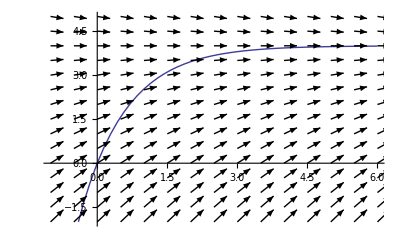

```mathematica
Show[p1,p2]
```

2. ẋ+3x=2	c.i. x(0)=4

```mathematica
DSolve[{x'[t]+3x[t]==2,x[0]==4},x[t],t]
```

{{x[t]→2/3 ⅇ^(-3 t) (5+ⅇ^(3 t))}}

```mathematica
Expand[%]
```

{{x[t]→2/3+(10 ⅇ^(-3 t))/3}}

```mathematica
p3=Plot[2/3(1+5 ⅇ^(-3t)),{t,0,8},PlotRange->{-1,4}];
```

```mathematica
p4=VectorFieldPlot[{18,-3x+2},{t,0,8},{x,-1,4}];
```

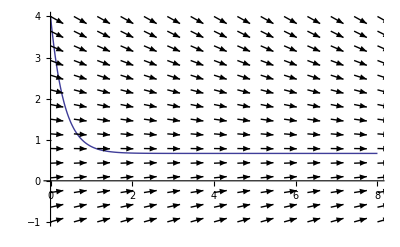

```mathematica
Show[p3,p4]
```

```mathematica
Clear[p1,p2,p3,p4]
```

3. ẋ+x=t	c.i. x(0)=4

```mathematica
sol1=DSolve[{x'[t]+x[t]==t,x[0]==4},x[t],t]
```

{{x[t]→ⅇ^-t (5-ⅇ^t+ⅇ^t t)}}

```mathematica
Simplify[%]
```

{{x[t]→-1+5 ⅇ^-t+t}}

4. ẋ-x=2t ⅇ^(2t)	donde x(0)=1

```mathematica
sol2=DSolve[{x'[t]-x[t]==2t ⅇ^(2t),x[0]==1},x[t],t]
```

{{x[t]→ⅇ^t (3-2 ⅇ^t+2 ⅇ^t t)}}

```mathematica
Expand[%]
```

{{x[t]→3 ⅇ^t-2 ⅇ^(2 t)+2 ⅇ^(2 t) t}}

5. tẋ-4x=t^6 ⅇ^t	donde x(1)=0

```mathematica
sol2=DSolve[{t x'[t]-4x[t]==t^6 ⅇ^t,x[1]==0},x[t],t]
```

{{x[t]→ⅇ^t (-1+t) t^4}}

```mathematica
Expand[%]
```

{{x[t]→-ⅇ^t t^4+ⅇ^t t^5}}

### Ecuaciones diferenciales de Bernoulli

Resuelva las siguientes ecuaciones diferenciales de Bernoulli.

1. ẋ+x=t x^2

```mathematica
DSolve[x'[t]+x[t]==t x[t]^2,x[t],t]
```

{{x[t]→1/(1+t+ⅇ^t C[1])}}

2. tẋ=-t^2 x^3

```mathematica
DSolve[{t x'[t]==-t^2x[t]^3},x[t],t]
```

{{x[t]→-1/(√(t^2-2 C[1]))},{x[t]→1/(√(t^2-2 C[1]))}}

3. t^2ẋ+2t x=5 x^2

```mathematica
DSolve[t^2 x'[t]+2t x[t]==5 x[t]^2,x[t],t]
```

{{x[t]→(3 t)/(5+3 t^3 C[1])}}

### Ecuaciones diferenciales de variables separables

Resuelva las siguientes ecuaciones diferenciales de variables separables.

1. ẋ=2x		c.i. x(0)=1

```mathematica
DSolve[{x'[t]==2x[t],x[0]==1},x[t],t]
```

{{x[t]→ⅇ^(2 t)}}

2. ẋ=x^3/t^3	c.i. x(1)=1

```mathematica
DSolve[{x'[t]==x[t]^3/t^3,x[1]==1},x[t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{x[t]→t}}

3. ẋ=(x-1)^2	c.i. x(0)=2

```mathematica
DSolve[{x'[t]==(x[t]-1)^2,x[0]==2},x[t],t]
```

{{x[t]→(-2+t)/(-1+t)}}

### Ejemplo de aplicación economico: Modelo de Evans

Considere las siguientes funciones de demanda y oferta de un bien en donde P denota el precio y Q la cantidad del bien:
D(t)=8-2p
S(t)=-2+p
Supongamos que P=P(t) es una función del tiempo y por lo tanto también Q lo es. El precio cambia en el tiempo de acuerdo con la ecuación diferencial y la condición inicial p(0)=5.
d/dtp(t)=j(D(t)-S(t))
a) Resolver la ecuación diferencial para p(t), cuando la velocidad de ajuste es j=0.1 y grafique la solución
b) Que sucede si j=0.9 y grafique
c) Cual es el precio de equilibrio o de estado estacionario
d) Grafique simultáneamente los dos primeros incisos y comente los resultados

```mathematica
DSolve[{p'[t]+(1/10)(2+1)p[t]==(1/10)(8+2),p[0]==5},p[t],t]
```

{{p[t]→5/3 ⅇ^(-3 t/10) (1+2 ⅇ^(3 t/10))}}

```mathematica
Expand[%]
```

{{p[t]→10/3+5/3 ⅇ^(-3 t/10)}}

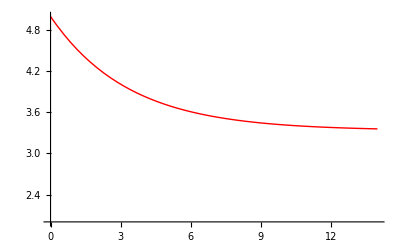

```mathematica
Plot[5/3(2+ⅇ^(-3t/10)),{t,0,14},PlotRange->{2,5},PlotStyle->RGBColor[1,0,0]]
```

```mathematica
DSolve[{p'[t]+(9/10)(2+1)p[t]==(9/10)(8+2),p[0]==5},p[t],t]
```

{{p[t]→5/3 ⅇ^(-27 t/10) (1+2 ⅇ^(27 t/10))}}

```mathematica
Expand[%]
```

{{p[t]→10/3+5/3 ⅇ^(-27 t/10)}}

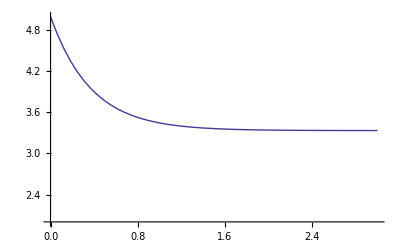

```mathematica
Plot[5/3(2+ⅇ^(-27t/10)),{t,0,3},PlotRange->{2,5}]
```

```mathematica
p1=Plot[5/3(2+ⅇ^(-3t/10)),{t,0,14},PlotRange->{2,5},PlotStyle->RGBColor[1,0,0]];
```

```mathematica
p2=Plot[5/3(2+ⅇ^(-27t/10)),{t,0,14},PlotRange->{2,5}];
```

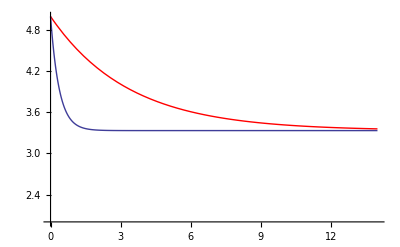

```mathematica
Show[p1,p2]
```

```mathematica
Clear[p1,p2]
```

### Ecuaciones diferenciales de segundo orden

Resuelva las siguientes ecuaciones diferenciales de segundo orden con termino variable

1. x^(..)+4ẋ+8x=16

```mathematica
DSolve[x''[t]+4x'[t]+8x[t]==16,x[t],t]
```

{{x[t]→2+ⅇ^(-2 t) C[2] Cos[2 t]+ⅇ^(-2 t) C[1] Sin[2 t]}}

2. x^(..)-2ẋ-3x=3ⅇ^(2t)

```mathematica
DSolve[x''[t]-2x'[t]-3x[t]==3 ⅇ^(2t),x[t],t]
```

{{x[t]→-ⅇ^(2 t)+ⅇ^-t C[1]+ⅇ^(3 t) C[2]}}

3. x^(..)-2ẋ+x=sen t

```mathematica
DSolve[x''[t]-2x'[t]+x[t]==Sin [t],x[t],t]
```

{{x[t]→ⅇ^t C[1]+ⅇ^t t C[2]+Cos[t]/2}}

### Ecuaciones diferenciales de orden superior

Resolver las siguientes ecuaciones diferenciales de orden superior

1. x^v-3 x^iv+3 x'''-3 x''+2 x'=0

```mathematica
DSolve[x'''''[t]-3x''''[t]+3x'''[t]-3x''[t]+2x'[t]==0,x[t],t]
```

{{x[t]→ⅇ^t C[3]+1/2 ⅇ^(2 t) C[4]+C[5]-C[2] Cos[t]+C[1] Sin[t]}}

2. x^iv-4 x'''+4 x''=0

```mathematica
DSolve[x''''[t]-4x'''[t]+4x''[t]==0,x[t],t]
```

{{x[t]→1/4 ⅇ^(2 t) (C[1]-C[2]+t C[2])+C[3]+t C[4]}}

3. x'''+x''-x'-x-1=0

```mathematica
DSolve[x'''[t]+x''[t]-x'[t]-x[t]-1==0,x[t],t]
```

{{x[t]→-1+ⅇ^-t C[1]+ⅇ^-t t C[2]+ⅇ^t C[3]}}

5. x'''+3 x''+3 x'+x=t^2+2t+1

```mathematica
DSolve[x'''[t]+3x''[t]+3x'[t]+x[t]==t^2+2t+1,x[t],t]
```

{{x[t]→7-4 t+t^2+ⅇ^-t C[1]+ⅇ^-t t C[2]+ⅇ^-t t^2 C[3]}}

### Ejemplo de aplicación económica a un modelo de mercado con expectativas de precio

En la formulación anterior del modelo dinámico de mercado, tanto D(t) como la S(t), se consideran funciones sólo del precio presente P(t). Pero algunas veces los compradores y los vendedores pueden basar su comportamiento de mercado no sólo en el precio presente sino también en la tendencia de precios que prevalece en el tiempo, ya que es probable que la tendencia de precios conduzca a ciertas expectativas respecto al nivel de precios en el futuro, y estas expectativas pueden a su vez influir en sus decisiones de oferta y demanda. Ósea;

D(t)=a-bp+mṗ+np^(..)	a,b>0
S(t)=-c+dp+uṗ+wp^(..)	c,d>0

Donde m y n son expectativas de demanda, si m>0 entonces aumenta la demanda presente porque los precios van a subir, caso contrario si m<0.

Ejemplo; Sean las ecuaciones de demanda y oferta respectivamente
D(t)=40-2p-2ṗ-p^(..)
S(t)=-5+3p
a) Encuentre P(t) con la hipótesis de que el mercado siempre esta en ceros con las condiciones iníciales p(0)=12 y ṗ(0)=1
b) Realice la grafica de p(t) y mencione que tipo de estabilidad tiene la función p(t)

```mathematica
d[p_]=40-2p[t]-2p'[t]-p''[t]
```

40-2 p[t]-2 p'[t]-p''[t]

```mathematica
s[p_]=-5+3p[t]
```

-5+3 p[t]

```mathematica
eq1=Simplify[d[p]-s[p]==0]
```

5 p[t]+2 p'[t]+p''[t]==45

```mathematica
sol=DSolve[{eq1,p[0]==12,p'[0]==1},p[t],t]
```

{{p[t]→ⅇ^-t (9 ⅇ^t+3 Cos[2 t]+2 Sin[2 t])}}

```mathematica
Expand[%]
```

{{p[t]→9+3 ⅇ^-t Cos[2 t]+2 ⅇ^-t Sin[2 t]}}

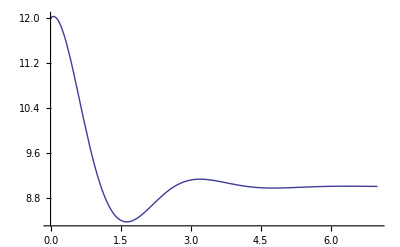

```mathematica
Plot[Evaluate[p[t]/.sol],{t,0,7},PlotRange->All]
```